```mathematica
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.csv"],Transpose@{
(Transpose@mydata["BackgroundFields"])[[1]],
(Transpose@mydata["BackgroundFields"])[[2]],
mydata["Alpha"],
mydata["Time"],
mydata["Radius"],
mydata["TimeDerivative"],
mydata["RadialDerivative"]},"CSV"];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.txt"],{{1,2,3},{10,20,30}},"List"];
```

```mathematica
Keys[mydata]
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

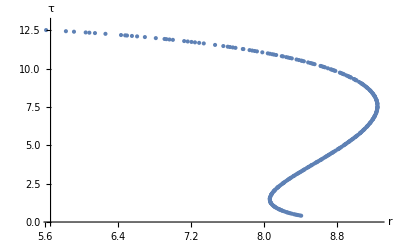

```mathematica
FreezeOutPlot=ListPlot[Transpose[{mydata["Radius"],mydata["Time"]}],AxesLabel->{r,τ}]
```

```mathematica
dalpha=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
ur=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]][[1;;-2]]]];
utau=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]][[1;;-2]]]];
```

```mathematica
Solve[a==(x+b)*(3*x-b)/(2*c),x]
```

{{x→1/3 (-b-√2 √(2 b^2+3 a c))},{x→1/3 (-b+√2 √(2 b^2+3 a c))}}

1.1547

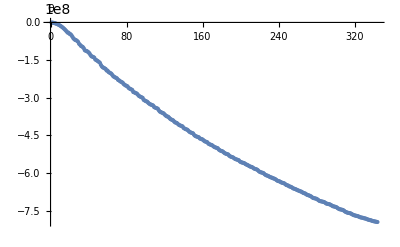

```mathematica
mσ=100*10^6;(*mass of the sigma field ~ O(10^2-10^3 MeV)???*)
ϵ=0.160054;(*energy density at freeze out*)
vev=1;(*vev of sigma field*)
χ2=(-mσ^2+2*mσ*Sqrt[3*ϵ/vev+mσ^2])/6;
χ=Sqrt[χ2];
θ0=0;

θ=θ0+χ*Accumulate[(mydata["TimeDerivative"][[1;;-2]]*utau-mydata["RadialDerivative"][[1;;-2]]*ur)*dalpha];
ρ=Sqrt[fπ*(2*χ2+mσ^2)/(mσ^2)]
ϕfreeze=ρ*Exp[I*θ];
ThetaPlot=ListPlot[θ,AxesLabel->{None,"θ"}]
```

```mathematica
Integrate[Exp[I*(a*Cos[x])],{x,0,2*Pi},Assumptions->Element[a,Reals]]
```

2 π BesselJ[0,Abs[a]]

```mathematica
rs=mydata["Radius"][[1;;-2]];
drs=mydata["RadialDerivative"][[1;;-2]];
taus=mydata["Time"][[1;;-2]];
dtaus=mydata["TimeDerivative"][[1;;-2]];
```

```mathematica
mπ=1;(* mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ω[p_]=Sqrt[p^2+mπ^2];
J0rp[p_]=BesselJ[0,rs*p];
J1rp[p_]=BesselJ[1,rs*p];
Y0tw[p_]=BesselY[0,taus*ω[p]];
Y1tw[p_]=BesselY[1,taus*ω[p]];
J0tw[p_]=BesselJ[0,taus*ω[p]];
J1tw[p_]=BesselJ[1,taus*ω[p]];
helper0[p_]=I*ϕfreeze*χ*(-drs*utau+dtaus*ur)*J0rp[p]*(-Y0tw[p]+I*J0tw[p]);
helper1[p_]=dtaus*p*J1rp[p]*(-Y0tw[p]+I*J0tw[p]);
helper2[p_]=drs*J0rp[p]*ω[p]*(Y1tw[p]-I*J0tw[p]);
ϕfourier[p_]=-I*2*Pi^2*Total[dalpha*taus*rs*(helper0[p]-ϕfreeze*(helper1[p]+helper2[p]))];
```

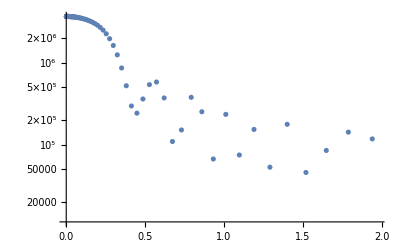

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
ps=logspace[-3,0.5,100];
ListLogPlot[Transpose@{ps,Abs[ϕfourier[ps]^2]}]
```